# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["/Users/pcs/Desktop/Entropy/Late time distributions/QMB.wl"];
```

MessageName::messg: TranslationEigenvectorRepresentatives::usage cannot be set to FormatUsage[TranslationEigenvectorRepresentatives[L] returns a list of sublists, each containing:  the decimal representation of a bit-string representative eigenvector,  its pseudomomentum k, and the length of its translation orbit,  for a system of ```L``` qubits.]. It must be set to a string.

MessageName::messg: BlockDiagonalize::usage cannot be set to FormatUsage[BlockDiagonalize[matrix,opts] returns ```matrix``` in block-diagonal form. Only 	option is '''Symmetry'''.]. It must be set to a string.

MessageName::messg: Transform::usage cannot be set to FormatUsage[Matrix transform for Translation symmetry]. It must be set to a string.

General::stop: Further output of MessageName::messg will be suppressed during this calculation.

```mathematica
LaunchKernels[10]
```

{Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel}

# Testing higher precision cycle

## Definitions

```mathematica
(*---your defs kept as-is---*)
ClearAll[revIndex,buildMaps,haar,ProjectBlockVector,evolveSector];
revIndex[i_,l_]:=FromDigits[Reverse[IntegerDigits[i,2,l]],2];
buildMaps[l_]:=Module[{visited,evenMap={},oddMap={},j},visited=ConstantArray[False,2^l,SparseArray];
Do[If[!visited[[idx+1]],j=revIndex[idx,l];
visited[[idx+1]]=True;visited[[j+1]]=True;
If[idx===j,AppendTo[evenMap,{idx}],AppendTo[evenMap,{idx,j}];AppendTo[oddMap,{idx,j}]]],{idx,0,2^l-1}];
{evenMap,oddMap}];
haar[L_Integer]:=Normalize@Table[SetPrecision[RandomVariate[NormalDistribution[0,1]],30]+I SetPrecision[RandomVariate[NormalDistribution[0,1]],30],{2^L}];
ProjectBlockVector[state_,map_,type_,l_]:=Module[{res,k=1,a,b},res=ConstantArray[0,Length[map]];
Do[If[Length[pair]==1,res[[k]]=state[[pair[[1]]+1]],{a,b}=pair;
res[[k]]=If[type==="even",(state[[a+1]]+state[[b+1]])/Sqrt[2],(state[[a+1]]-state[[b+1]])/Sqrt[2]]];
k++,{pair,map}];
res];
evolveSector[evec_,eval_,state_,t_]:=Module[{ck=Conjugate[evec].state},Total[(ck*Exp[-I eval*t])*evec]];
pageEntropy[La_,Lb_]:=PolyGamma[0,(2^La)(2^Lb)+1]-PolyGamma[0,(2^Lb)+1]-((2^La)-1)/(2*(2^Lb));
```

## Method

```mathematica
(*---parameters/data shared---*)
L=4;
{evenMap,oddMap}=buildMaps[L];
J=SetPrecision[1,30];
g=SetPrecision[1,30];
tlist=Table[SetPrecision[10^τ,30],{τ,-2,22,0.0020}];
hlist=Reverse@Sort@Append[Table[SetPrecision[10^x,30],{x,-8,0,0.5}],0];
```

```mathematica
tlist//Length
hlist//Length
```

12001

18

```mathematica
BlockRandom[SeedRandom[1234]];
state=Flatten[KroneckerProduct[haar[L/2],haar[L/2]],1];
dims={2^(L/2),2^(L/2)};
```

```mathematica
(*---loop over hlist on the master;parallelize only inner maps---*)
data=Table[

Module[{h=hlist[[q]],Ha,eigenval,eigenvec,ord,evolution,schmidts,entropy},

Ha=IsingHamiltonian[g,h,J,L,BoundaryConditions->"Open"];
{eigenval,eigenvec}=Quiet[Eigensystem[Ha]];
ord=Ordering[eigenval];
eigenval=eigenval[[ord]];
eigenvec=eigenvec[[ord]];(*Orthogonalize[eigenvec] if needed*)(*ship*numerical*arrays+helper≥only*)DistributeDefinitions[evolveSector,eigenvec,eigenval,state];
evolution=ParallelMap[evolveSector[eigenvec,eigenval,state,#]&,tlist];
schmidts=ParallelMap[SingularValueList[ArrayReshape[#,dims],Tolerance->0]&,Chop[evolution,10^(-23)]];
entropy=Table[Total[If[#==0,0,-# Log[#]]&/@(i^2)],{i,schmidts}]]

,{q,Length[hlist]}];
Export["entanglement_high_precision_L_"<>ToString[L]<>"_J_h_1_LRN.m",data]
```

```mathematica
data//Dimensions
```

{14,9601}

```mathematica
n=Length[hlist]+1;
reds=Reverse[Table[Blend[{RGBColor[0.1,0.1,1],RGBColor[1,0,0]},t],{t,1/(n-1),1,1/(n-1)}]];
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
```

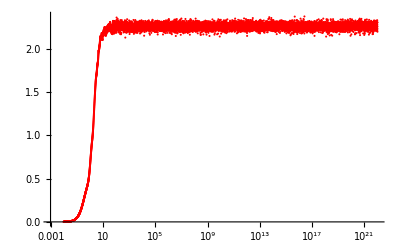

```mathematica
q=1;
ListLogLinearPlot[Transpose[{tlist,data[[q]]}],PlotRange->All,PlotStyle->reds[[q]]]
```

```mathematica
data=Import["/Users/pcs/Desktop/Entropy/Late time distributions/entanglement_high_precision_L_10_J_g_1_SRN.m"];
```

```mathematica
pageplot=LogLinearPlot[pageEntropy[5,5],{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Black,Dashed,Thick]];
```

```mathematica
Show[{Show[Table[ListLogLinearPlot[{Transpose[{tlist,data[[q]]}],MovingAverage[Transpose[{tlist,data[[q]]}],100]},PlotRange->All,PlotStyle->{Directive[Gray,Opacity[0.075]],Directive[reds[[q]]]},PlotRange->All,ImageSize->1200,FrameStyle->Directive[Black,20],PlotTheme->"Detailed",GridLines->Automatic,FrameLabel->{Style["t",Black,25],Style["S(t)",Black,25]},PlotLabel->Style["SRN, L = 8",30,Black]],{q,Length[hlist]-1}]],pageplot}]
```

```mathematica
(*---parameters/data shared---*)
L=10;
{evenMap,oddMap}=buildMaps[L];
J=SetPrecision[1,30];
g=SetPrecision[1,30];
tlist=Table[SetPrecision[10^τ,30],{τ,-2,22,0.0020}];
hlist=Reverse@Sort@Append[Table[SetPrecision[10^x,30],{x,-8,0,0.5}],0];
BlockRandom[SeedRandom[1234]];
state=Flatten[KroneckerProduct[haar[L/2],haar[L/2]],1];
dims={2^(L/2),2^(L/2)};
```

```mathematica
(*---loop over hlist on the master;parallelize only inner maps---*)
data=Table[
Module[{h=hlist[[q]],Ha,eigenval,eigenvec,ord,evolution,schmidts,entropy},
Ha=IsingHamiltonian[g,h,J,L,BoundaryConditions->"Open"];
{eigenval,eigenvec}=Quiet[Eigensystem[Ha]];
ord=Ordering[eigenval];
eigenval=eigenval[[ord]];
eigenvec=eigenvec[[ord]];(*Orthogonalize[eigenvec] if needed*)(*ship*numerical*arrays+helper≥only*)DistributeDefinitions[evolveSector,eigenvec,eigenval,state];
evolution=ParallelMap[evolveSector[eigenvec,eigenval,state,#]&,tlist];
schmidts=ParallelMap[SingularValueList[ArrayReshape[#,dims],Tolerance->0]&,Chop[evolution,10^(-23)]];
entropy=Table[Total[If[#==0,0,-# Log[#]]&/@(i^2)],{i,schmidts}]]
,{q,Length[hlist]}];
Export["entanglement_high_precision_L_"<>ToString[L]<>"_J_h_1_LRN.m",data]
```